## Legendre Polynomials and Function Expansion

```mathematica
??LegendreP
```

RowBox[{"LegendreP", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["x", "TI"]}], "]"}] gives the Legendre polynomial RowBox[{SubscriptBox["P", "n"], "(", StyleBox["x", "TI"], ")"}]. 
RowBox[{"LegendreP", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["m", "TI"], ",", StyleBox["x", "TI"]}], "]"}] gives the associated Legendre polynomial RowBox[{SubsuperscriptBox["P", "n", "m"], "(", StyleBox["x", "TI"], ")"}].

Attributes[LegendreP]={Listable,NumericFunction,Protected,ReadProtected}

### Legendre Polynomials on the interval [-1,1]

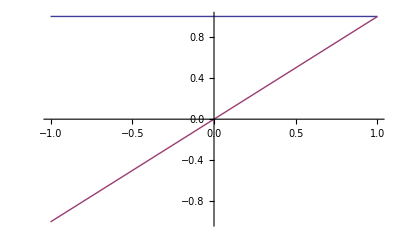

```mathematica
Plot[{LegendreP[0,x],LegendreP[1,x]},{x,-1,1}]
```

```mathematica
LegendreP[0,x]
```

1

```mathematica
LegendreP[1,x]
```

x

```mathematica
∫_-1^1 LegendreP[0,x]ⅆx
∫_-1^1 LegendreP[0,x]^2 ⅆx
```

2

2

```mathematica
∫_-1^1 LegendreP[1,x]ⅆx
∫_-1^1 LegendreP[1,x]^2 ⅆx
```

0

2/3

```mathematica
∫_-1^1 LegendreP[0,x]LegendreP[1,x]ⅆx
```

0

We see that these functions are orthogonal on the interval [-1,1]

### Legendre Polynomials on the interval [-a,a]

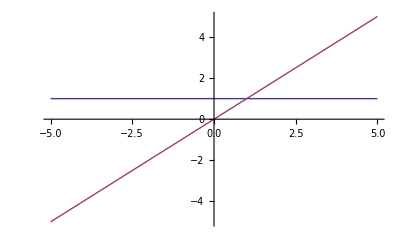

```mathematica
Plot[{LegendreP[0,x],LegendreP[1,x]},{x,-5,5}]
```

```mathematica
∫_-a^a LegendreP[0,x]ⅆx
∫_-a^a LegendreP[0,x]^2 ⅆx
```

2 a

2 a

```mathematica
∫_-a^a LegendreP[1,x]ⅆx
∫_-a^a LegendreP[1,x]^2 ⅆx
```

0

(2 a^3)/3

```mathematica
∫_-a^a LegendreP[0,x]LegendreP[1,x]ⅆx
```

0

### Legendre Polynomials on the interval [a,b]

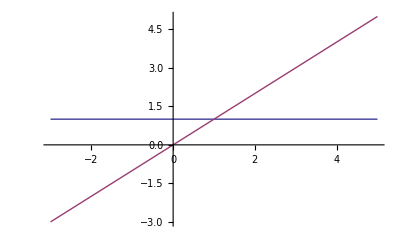

```mathematica
Plot[{LegendreP[0,x],LegendreP[1,x]},{x,-3,5}]
```

```mathematica
∫_a^b LegendreP[0,x]^2 ⅆx
```

-a+b

```mathematica
∫_a^b LegendreP[1,x]^2 ⅆx
```

-a^3/3+b^3/3

```mathematica
∫_a^b LegendreP[0,x]LegendreP[1,x]ⅆx
```

-a^2/2+b^2/2

### Normalized Legendre Polynomials

We want our Legendre Polynomials to be normalized such that ∫_a^b LegendreP[n,x]ⅆx = 1.

```mathematica
LegendreP[0,x]
LegendreP[1,x]
```

1

x

```mathematica
Subscript[α, 0]∫_a^b LegendreP[0,x]^2 ⅆx
Subscript[α, 1]∫_a^b LegendreP[1,x]^2 ⅆx
```

(-a+b) α_0

(-a^3/3+b^3/3) α_1

```mathematica
Solve[Subscript[α, 0]∫_a^b LegendreP[0,x]^2 ⅆx==1,Subscript[α, 0]]
Solve[Subscript[α, 1]∫_a^b LegendreP[1,x]^2 ⅆx==1,Subscript[α, 1]]
```

{{α_0→1/(-a+b)}}

{{α_1→-3/(a^3-b^3)}}

Here is a Legendre Polynomial normlaized over the interval [a,b]

```mathematica
∫_a^b LegendreP[1,x]^2 ⅆx
```

-a^3/3+b^3/3

LP is our normalized Legendre Polynomials

```mathematica
LP[n_,x_,a_:-1,b_:1] :=LegendreP[n,x]/((∫_a^b LegendreP[n,x]^2 ⅆx)^(1/2))
```

```mathematica
LP[0,x]
LP[1,x]
```

1/(√2)

√(3/2) x

```mathematica
∫_-1^1 LP[0,x]^2 ⅆx
∫_-1^1 LP[1,x]^2 ⅆx
```

1

1

```mathematica
LP[0,x]^2
LP[1,x]^2
```

1/2

(3 x^2)/2

```mathematica
∫_-1^1 LP[0,x]LP[1,x]ⅆx
```

0

```mathematica
∫_a^b LP[0,x,a,b]LP[1,x,a,b]ⅆx
```

(√3 (-a^2+b^2))/(2 √(-a+b) √(-a^3+b^3))

```mathematica
∫_a^b LP[0,x,a,b]LP[1,x,a,b]ⅆx/.{a->-1.,b->2.}
```

0.5

```mathematica
∫_a^b LP[0,x,a,b]LP[1,x,a,b]ⅆx/.{a->-2.,b->2.}
```

0.

We see that the Legendre Polynomials are orthogonal to each other as long as they are centered about 0.

### Centered Legendre Polynomials

Legendre Polynomials are only orthogonal to each other when they are centered about 0.  Unfortunately, my bins will not be centered about 0 so I have to shift the polynomial.  In this section my bin will go from [1,5], and therefore it's midpoint is at 3.

```mathematica
LegendreP[0,x-3.]
LegendreP[1,x-3.]
```

1.

-3.+1. x

```mathematica
∫_-2^2 LegendreP[0,x-3.]LegendreP[1,x-3.]ⅆx
```

-12.

```mathematica
∫_1^5 LegendreP[0,x-3.]LegendreP[1,x-3.]ⅆx
```

0.

```mathematica
(*Centered Legendre Polynomial*)Clp[n_,x_,xmin_,xmax_]:=LegendreP[n,x-(xmax+xmin)/2]
```

```mathematica
Clp[0,x,-1,1]
LegendreP[0,x]
```

1

1

```mathematica
Clp[1,x,a,b]
```

0.-0.5 a-0.5 b+1. x

```mathematica
∫_1^5 Clp[0,x,1,5]Clp[1,x,1,5]ⅆx
```

0.

```mathematica
∫_a^b Clp[0,x,a,b]Clp[1,x,a,b]ⅆx
∫_a^b Clp[0,x,a,b]Clp[0,x,a,b]ⅆx
∫_a^b Clp[1,x,a,b]Clp[1,x,a,b]ⅆx
```

0

-a+b

-1/12 (a-b)^3

```mathematica
Simplify[%]
```

0. a^2+a (0.+0. b)+0. b+0. b^2

```mathematica
∫_(a-(a+b)/2)^(b-(a+b)/2) LegendreP[0,x]LegendreP[1,x]ⅆx
∫_(a-(a+b)/2)^(b-(a+b)/2) LegendreP[0,x]LegendreP[0,x]ⅆx
∫_(a-(a+b)/2)^(b-(a+b)/2) LegendreP[1,x]LegendreP[1,x]ⅆx
```

0

-a+1/2 (-a-b)+b+(a+b)/2

-1/12 (a-b)^3

```mathematica
IP[n_,m_] :=∫_a^b Clp[n,x,a,b]Clp[m,x,a,b]ⅆx
```

```mathematica
IP2[n_,m_]:=∫_-b^b LegendreP[n,x]LegendreP[m,x]ⅆx
```

```mathematica
IP2[0,0]
IP2[1,1]
IP2[1,0]
```

2 b

(2 b^3)/3

0

```mathematica
T = Table[IP2[i,j],{i,5},{j,5}]
```

{{(2 b^3)/3,0,-b^3+b^5,0,(5 b^3)/4-(7 b^5)/2+(9 b^7)/4},{0,b/2-b^3+(9 b^5)/10,0,-(3 b)/8+(13 b^3)/8-(25 b^5)/8+(15 b^7)/8,0},{-b^3+b^5,0,(3 b^3)/2-3 b^5+(25 b^7)/14,0,-(15 b^3)/8+(57 b^5)/8-(77 b^7)/8+(35 b^9)/8},{0,-(3 b)/8+(13 b^3)/8-(25 b^5)/8+(15 b^7)/8,0,(9 b)/32-(15 b^3)/8+(111 b^5)/16-(75 b^7)/8+(1225 b^9)/288,0},{(5 b^3)/4-(7 b^5)/2+(9 b^7)/4,0,-(15 b^3)/8+(57 b^5)/8-(77 b^7)/8+(35 b^9)/8,0,(75 b^3)/32-(105 b^5)/8+(485 b^7)/16-(245 b^9)/8+(3969 b^11)/352}}

```mathematica
T//MatrixForm
```

((2 b^3)/3 | 0 | -b^3+b^5 | 0 | (5 b^3)/4-(7 b^5)/2+(9 b^7)/4
0 | b/2-b^3+(9 b^5)/10 | 0 | -(3 b)/8+(13 b^3)/8-(25 b^5)/8+(15 b^7)/8 | 0
-b^3+b^5 | 0 | (3 b^3)/2-3 b^5+(25 b^7)/14 | 0 | -(15 b^3)/8+(57 b^5)/8-(77 b^7)/8+(35 b^9)/8
0 | -(3 b)/8+(13 b^3)/8-(25 b^5)/8+(15 b^7)/8 | 0 | (9 b)/32-(15 b^3)/8+(111 b^5)/16-(75 b^7)/8+(1225 b^9)/288 | 0
(5 b^3)/4-(7 b^5)/2+(9 b^7)/4 | 0 | -(15 b^3)/8+(57 b^5)/8-(77 b^7)/8+(35 b^9)/8 | 0 | (75 b^3)/32-(105 b^5)/8+(485 b^7)/16-(245 b^9)/8+(3969 b^11)/352)

```mathematica
FullSimplify[T]//MatrixForm
```

((2 b^3)/3 | 0 | b^3 (-1+b^2) | 0 | 1/4 b^3 (5-14 b^2+9 b^4)
0 | 1/10 b (5-10 b^2+9 b^4) | 0 | 1/8 b (-3+13 b^2-25 b^4+15 b^6) | 0
b^3 (-1+b^2) | 0 | (3 b^3)/2-3 b^5+(25 b^7)/14 | 0 | 1/8 b^3 (-15+57 b^2-77 b^4+35 b^6)
0 | 1/8 b (-3+13 b^2-25 b^4+15 b^6) | 0 | 1/288 b (81-540 b^2+1998 b^4-2700 b^6+1225 b^8) | 0
1/4 b^3 (5-14 b^2+9 b^4) | 0 | 1/8 b^3 (-15+57 b^2-77 b^4+35 b^6) | 0 | 1/352 b^3 (825-4620 b^2+10670 b^4-10780 b^6+3969 b^8))

Clearly these are not all orthogonal so my derivation is not correct.

### Normalized and Centered Legendre Polynomials

If we combine normalized and centered polynomials we finally have our desired product.  It is important to not that the Legendre Polynomial must first be centered and then normalized.

```mathematica
LPc[n_,x_,a_:-1,b_:1] :=LegendreP[n,x-(b+a)/2.]/((∫_a^b LegendreP[n,x-(b+a)/2.]^2 ⅆx)^(1/2))
```

```mathematica
LPc[0,x,1.,5]
Expand[LPc[1,x,1.,5]]
```

0.5

-1.29904+0.433013 x

```mathematica
N[%]
```

0.433013 (-3.+1. x)

```mathematica
∫_1^5 LPc[0,x,1.,5.]^2 ⅆx
∫_1^5 LPc[1,x,1.,5.]^2 ⅆx
```

1.

1.

```mathematica
LPc[0,x,a,b]
LPc[1,x,a,b]
```

1./(√(-a+b))

(0.-0.5 a-0.5 b+1. x)/(√(-0.0833333 a^3+0.25 a^2 b-0.25 a b^2+0.0833333 b^3))

```mathematica
∫_a^b LPc[0,x,a,b]^2 ⅆx
∫_a^b LPc[1,x,a,b]^2 ⅆx
```

1.

1

```mathematica
∫_-1^2 LPc[1,x,-1,2]^2 ⅆx
```

1.

```mathematica
Simplify[%]
```

1.

```mathematica
∫_1^5 LPc[0,x,1,5]LPc[1,x,1,5]ⅆx
```

0.

## Holloway's "Manual" Version

```mathematica
f[x_,n_:2]:=∑_(j=1)^n Subscript[a, j] LegendreP[x,j]
f[x]
```

a_1+LegendreP[x,2] a_2

```mathematica
g[x_]:=0.5*(1+x) (*Function we want to approximate*)
U[x_]:=0.5 (*Uniform sampling probability*)
ω[x_]:= g[x]/U[x](*Weighting function*)
```

```mathematica
ω[x]
```

1. (1+x)

```mathematica
k[n_]:=2/(2*n+1)
```

```mathematica
r=Table[Random[Real,{-1,1}],{i,10}];
```

```mathematica
Dynamic[1/k[0] Mean[Map[ω,r]]]
Dynamic[1/k[1] Mean[Map[ω,r]*r]]
```

Yeah this is what we expect to get.  Of course this is the easiest sample because it has the same domain as the Legendre Polynomials.

## Griesheimer Version of Normalized and Centered Legendre Polynomials

The scaled version of x:

### Scaling, Orthogonalization, and Normalization

```mathematica
xScaled[x_,xmin_,xmax_]:=2*((x-xmin)/(xmax-xmin))-1
k[n_,xmin_,xmax_]:=(2n+1)/(xmax-xmin)
k[n_] := (2n+1)/2
```

```mathematica
LPScaled[n_,x_,xmin_,xmax_]:=LegendreP[n,xScaled[x,xmin,xmax]]
```

```mathematica
LegendreP[0,xScaled[x,1,5]]
LegendreP[1,xScaled[x,1,5]]
```

1

1/2 (-3+x)

```mathematica
∫_xmin^xmax LPScaled[0,x,xmin,xmax]LPScaled[1,x,xmin,xmax]ⅆx
```

0

```mathematica
∫_1^5 LPScaled[0,x,1,5]LPScaled[1,x,1,5]ⅆx
```

0

So the scaled Legendre polynomials are naturally orthogonal

```mathematica
∫_xmin^xmax LPScaled[0,x,xmin,xmax]^2 ⅆx
∫_xmin^xmax LPScaled[1,x,xmin,xmax]^2 ⅆx
```

xmax-xmin

xmax/3-xmin/3

```mathematica
∫_1^5 LPScaled[0,x,1,5]^2 ⅆx
∫_1^5 LPScaled[1,x,1,5]^2 ⅆx
```

4

4/3

But not naturally normal

```mathematica
k[0,xmin,xmax]∫_xmin^xmax LPScaled[0,x,xmin,xmax]^2 ⅆx
Simplify[k[1,xmin,xmax]∫_xmin^xmax LPScaled[1,x,xmin,xmax]^2 ⅆx]
```

1

1

```mathematica
k[0,1,5]∫_1^5 LPScaled[0,x,1,5]^2 ⅆx
k[1,1,5]∫_1^5 LPScaled[1,x,1,5]^2 ⅆx
```

1

1

Adding the normalization constant k_nmakes the function normal and orthgonal

```mathematica
LPNS[n_,x_,xmin_,xmax_]:=√k[n,xmin,xmax] LPScaled[n,x,xmin,xmax]
```

LPNS[n,x,x_min,x_max] is a scaled, orthonormal function.

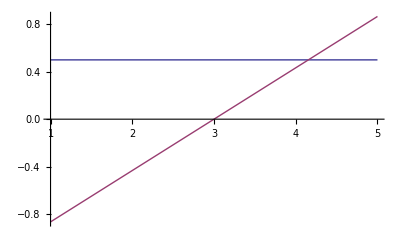

```mathematica
Plot[{LPNS[0,x,1,5],LPNS[1,x,1,5]},{x,1,5},PlotStyle->Thick]
```

```mathematica
LPNS[0,x,1,5]
```

0.5

```mathematica
LPScaled[0,x,1,6]
```

1.

```mathematica
LPScaled[1,x,1,6]
```

-1.4+0.4 x

```mathematica
xScaled[x,1,6]
```

-1.+0.4 (-1+x)

```mathematica
∫_a^b LPNS[0,x,a,b]^2 ⅆx
∫_a^b LPNS[1,x,a,b]^2 ⅆx
```

1.

1

```mathematica
Simplify[∫_a^b LPNS[0,x,a,b]LPNS[1,x,a,b]ⅆx]
```

(0. a^2+0. a b+0. b^2)/((a-1. b) (-1. a+b))

### Functional Expansion of scaled Legendre Polynomials

```mathematica
f[N_,x_,xmin_,xmax_]:=∑_(n=0)^(N-1) Subscript[α, n]*LPNS[n,x,xmin,xmax]
```

```mathematica
f[2,x,a,b]
```

1. √(1/(-a+b)) α_0+(√3 √(1/(-a+b)) (-1. a-1. b+2. x) α_1)/(-1. a+b)

```mathematica
A=∫_a^b f[2,x,a,b]LPNS[0,x,a,b]ⅆx
```

((-1. a^2+2. a b-1. b^2) α_0+(0. a^2+0. a b+0. b^2) α_1)/((a-1. b) (-1. a+b))

```mathematica
FactorTerms[A]
```

((-1. a^2+2. a b-1. b^2) α_0+(0. a^2+0. a b+0. b^2) α_1)/((a-1. b) (-1. a+b))

```mathematica
FactorTerms[A/.Subscript[α, 1]->0]
```

((-1. a^2+2. a b-1. b^2) α_0)/((a-1. b) (-1. a+b))

```mathematica
Simplify[%]
```

((-1. a^2+2. a b-1. b^2) α_0)/((a-1. b) (-1. a+b))

```mathematica
Expand[-(a-b)^2]
```

-a^2+2 a b-b^2

```mathematica
Expand[-(a-b)^2]/((a-b)(b-a))Subscript[α, 0]
```

((-a^2+2 a b-b^2) α_0)/((a-b) (-a+b))

```mathematica
Simplify[%]
```

α_0

It's not obvious, but A=a_0.

```mathematica
B=∫_a^b f[2,x,a,b]LPNS[1,x,a,b]ⅆx
```

-(1.73205 ((0. a^3+0. a^2 b+0. a b^2+0. b^3) α_0+(-0.57735 a^3+1.73205 a^2 b-1.73205 a b^2+0.57735 b^3) α_1))/((a-1. b) (-1. a+b)^2)

```mathematica
FactorTerms[B/.Subscript[α, 0]->0]
```

-(1.73205 (-0.57735 a^3+1.73205 a^2 b-1.73205 a b^2+0.57735 b^3) α_1)/((a-1. b) (-1. a+b)^2)

```mathematica
Factor[-0.57735 a^3+1.73205 a^2 b-1.73205 a b^2+0.57735 b^3]
```

-0.57735 (1. a^3-3. a^2 b+3. a b^2-1. b^3)

```mathematica
Expand[(a-b)^3]
```

a^3-3 a^2 b+3 a b^2-b^3

```mathematica
Simplify[Expand[(a-b)(b-a)^2]]
```

(a-b)^3

```mathematica
(1.73205*0.57735(a-b)^3)/(a-b)^3 Subscript[α, 1]
```

0.999999 α_1

Again it's not obvious but B=α_1.

So if my Legendre polynomials are properly normalized and scaled then everything works out perfectly.

```mathematica
LPScaled[0,x,1,5]
LPScaled[1,x,1,5]
```

1.

-1.5+0.5 x

```mathematica
k[0,1,5]
k[1,1,5]
```

1/4

3/4

```mathematica
LPNS[0,x,-1,1]
```

0.707107

```mathematica
Sqrt[2.]/2
```

0.707107

```mathematica
k[0,-1,1]
```

1/2

```mathematica
LPNS[0,x,-1,1]/(√k[0,-1,1])
```

1.

```mathematica
LPScaled[0,x,-1,1]
```

1.

```mathematica
r=Table[Random[Real,{-1,1}],{i,1000000}];
```

```mathematica
Dynamic[Mean[LPScaled[0,r,-1,1]]]
Dynamic[Mean[LPScaled[1,r,-1,1]]]
```

## Normalizing a linear function

```mathematica
f[x_,m_,b_]:=m*x+b
```

```mathematica
∫_xmin^xmax f[x,m,b]^2 ⅆx
```

((b+m xmax)^3-(b+m xmin)^3)/(3 m)

```mathematica
a=∫_xmin^xmax f[x,m,b]ⅆx;
Simplify[a]
```

1/2 (xmax-xmin) (2 b+m (xmax+xmin))

```mathematica
fN[x_,m_,b_,xmin_,xmax_,n_:2]:=f[x,m,b]/((∫_xmin^xmax f[x,m,b]^n ⅆx)^(1/n))
```

```mathematica
fN[x,1,-1,1,5]
```

1/8 √3 (-1+x)

```mathematica
Expand[fN[x,1.0,0.0,0,5,1]]
Expand[fN[x,1.0,0.0,0,5,2]]
```

0.+0.08 x

0.+0.154919 x

```mathematica
∫_0^5 f[x,1.,0]ⅆx
```

12.5

```mathematica
∫_1^5 fN[x,1,-1,1,5,2]^2 ⅆx
∫_1^5 fN[x,1,-1,1,5,1]ⅆx
```

1

1

```mathematica
N[fN[x,1,-1,1,5]]
```

0.046875 (-1.+x)

```mathematica
Expand[fN[x,0.0234,-1.1719,1,5]]
```

-0.241236+0.0048169 x

```mathematica
Expand[fN[x,1,-1,1,5]]
```

-3/64+(3 x)/64

```mathematica
N[%]
```

-0.046875+0.046875 x

```mathematica
Expand[fN[x,0.5,0.5,-1,1]]
```

0.75+0.75 x

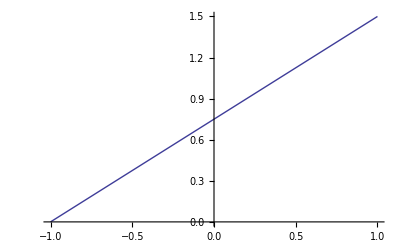

```mathematica
Plot[0.75*(x+1),{x,-1,1}]
```

```mathematica
Expand[fN[x,0.75,0.75, -1,1,2]]
```

0.5+0.5 x

```mathematica
Expand[fN[x,1,-1,1,5.,2]]
```

-0.046875+0.046875 x

## Let's look at an example

#### Set up function

Piecewise[{{1.+0.666667 x, 0≤x<3}, {6.-x, 3≤x<5}, {1., 5≤x<7}, {4.5-0.5 x, 7≤x<12}, {-1.5, 12≤x<15}, {-21.5+1.33333 x, 15≤x<18}, {11.5-0.5 x, 18≤x<20}, {5.5-0.2 x, 20≤x<23}, {0.9, 23≤x<26}, {-4.3+0.2 x, 26≤x<30}}]

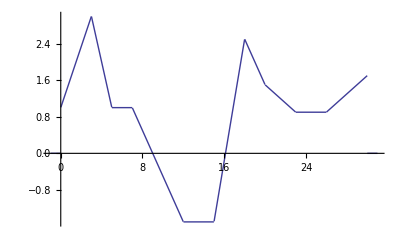

```mathematica
Subscript[f, 1][x_] := 1.+2./3. x
Subscript[f, 2][x_] := 6.-x
Subscript[f, 3][x_] := 1.
Subscript[f, 4][x_]:=4.5-1./2. x
Subscript[f, 5][x_]:=-1.5
Subscript[f, 6][x_] := -21.5+4./3. x
Subscript[f, 7][x_]:=11.5-1./2. x
Subscript[f, 8][x_]:=5.5-1./5. x
Subscript[f, 9][x_]:=0.9
Subscript[f, 10][x_]:=-4.3+1./5. x
f[x_] = Piecewise[{
{Subscript[f, 1][x],0≤x<3},
{Subscript[f, 2][x],3≤x<5},
{Subscript[f, 3][x],5≤x<7},
{Subscript[f, 4][x],7≤x<12},
{Subscript[f, 5][x],12≤x<15},
{Subscript[f, 6][x],15≤x<18},
{Subscript[f, 7][x],18≤x<20},
{Subscript[f, 8][x],20≤x<23},
{Subscript[f, 9][x],23≤x<26},
{Subscript[f, 10][x],26≤x<30}},0]
Plot[f[x],{x,-1,31}, PlotRange->All]
```

```mathematica
∫_0^3 Abs[Subscript[f, 1][x]]ⅆx
∫_3^5 Abs[Subscript[f, 2][x]]ⅆx
∫_5^7 Abs[Subscript[f, 3][x]]ⅆx
∫_7^12 Abs[Subscript[f, 4][x]]ⅆx
∫_12^15 Abs[Subscript[f, 5][x]]ⅆx
∫_15^18 Abs[Subscript[f, 6][x]]ⅆx
∫_18^20 Abs[Subscript[f, 7][x]]ⅆx
∫_20^23 Abs[Subscript[f, 8][x]]ⅆx
∫_23^26 Abs[Subscript[f, 9][x]]ⅆx
∫_26^30 Abs[Subscript[f, 10][x]]ⅆx
```

6.

4.

2.

3.25

4.5

3.1875

4.

3.6

2.7

5.2

#### Now what about the big picture?

Make PDF by making each bin have the value of the probability of sampling from each bin. In the following analysis, there are two approaches.  One is used and the other has been commented out.  The difference is simply multiplying and dividing by the width of the bin.  Since I have a discrete probability, I can't use Mathematica's integration because, by definition of an integral, will multiply by the width of the bin.

Normalization constant, H

```mathematica
h[x_]:=Piecewise[{
{∫_0^3 Abs[Subscript[f, 1][t]]ⅆt,0≤x<3},
{∫_3^5 Abs[Subscript[f, 2][t]]ⅆt,3≤x<5},
{∫_5^7 Abs[Subscript[f, 3][t]]ⅆt,5≤x<7},
{∫_7^12 Abs[Subscript[f, 4][t]]ⅆt,7≤x<12},
{∫_12^15 Abs[Subscript[f, 5][t]]ⅆt,12≤x<15},
{∫_15^18 Abs[Subscript[f, 6][t]]ⅆt,15≤x<18},
{∫_18^20 Abs[Subscript[f, 7][t]]ⅆt,18≤x<20},
{∫_20^23 Abs[Subscript[f, 8][t]]ⅆt,20≤x<23},
{∫_23^26 Abs[Subscript[f, 9][t]]ⅆt,23≤x<26},
{∫_26^30 Abs[Subscript[f, 10][t]]ⅆt,26≤x<30}},0]
H = h[0]+h[3]+h[5]+h[7] +h[12]+h[15]+h[18]+h[20]+h[23]+h[26]+h[30]
h[x]
```

38.4375

Piecewise[{{6., 0≤x<3}, {4., 3≤x<5}, {2., 5≤x<7}, {3.25, 7≤x<12}, {4.5, 12≤x<15}, {3.1875, 15≤x<18}, {4., 18≤x<20}, {3.6, 20≤x<23}, {2.7, 23≤x<26}, {5.2, 26≤x<30}}]

```mathematica
Simplify[f[x]/H]
```

Piecewise[{{-0.0390244, 12≤x<15}, {0.0234146, 23≤x<26}, {0.0260163, 5≤x<7}, {0.156098-0.0260163 x, 3≤x<5}, {0.117073-0.0130081 x, 7≤x<12}, {0.299187-0.0130081 x, 18≤x<20}, {0.143089-0.00520325 x, 20≤x<23}, {-0.11187+0.00520325 x, 26≤x<30}, {0.0260163+0.0173442 x, 0≤x<3}, {-0.55935+0.0346883 x, 15≤x<18}}]

```mathematica
f6[x_]:=Simplify[(Subscript[f, 6][x])/H]
```

```mathematica
f6[x]
```

-0.55935+0.0346883 x

```mathematica
f6[15.1]
```

-0.0355556

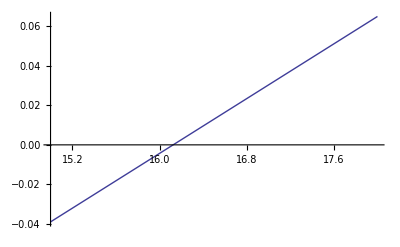

```mathematica
Plot[f6[x],{x,15,18}]
```

```mathematica
p[x_] :=h[x]/H
P[x_]:=Piecewise[{
{p[0],0≤x<3},
{p[0]+p[3],3≤x<5},
{p[0]+p[3]+p[5],5≤x<7},
{p[0]+p[3]+p[5]+p[7],7≤x<12},
{p[0]+p[3]+p[5]+p[7]+p[12],12≤x<15},
{p[0]+p[3]+p[5]+p[7]+p[12]+p[15],15≤x<18},
{p[0]+p[3]+p[5]+p[7]+p[12]+p[15]+p[18],18≤x<20},
{p[0]+p[3]+p[5]+p[7]+p[12]+p[15]+p[18]+p[20],20≤x<23},
{p[0]+p[3]+p[5]+p[7]+p[12]+p[15]+p[18]+p[20]+p[23],23≤x<26},
{p[0]+p[3]+p[5]+p[7]+p[12]+p[15]+p[18]+p[20]+p[23]+p[26],26≤x<30}},0]
Simplify[p[x]]
P[x]
```

Piecewise[{{0.0520325, 5≤x<7}, {0.0702439, 23≤x<26}, {0.0829268, 15≤x<18}, {0.0845528, 7≤x<12}, {0.0936585, 20≤x<23}, {0.104065, 3≤x<5||18≤x<20}, {0.117073, 12≤x<15}, {0.135285, 26≤x<30}, {0.156098, 0≤x<3}}]

Piecewise[{{0.156098, 0≤x<3}, {0.260163, 3≤x<5}, {0.312195, 5≤x<7}, {0.396748, 7≤x<12}, {0.513821, 12≤x<15}, {0.596748, 15≤x<18}, {0.700813, 18≤x<20}, {0.794472, 20≤x<23}, {0.864715, 23≤x<26}, {1., 26≤x<30}}]

```mathematica
p[x]
```

0.0260163 (Piecewise[{{6., 0≤x<3}, {4., 3≤x<5}, {2., 5≤x<7}, {3.25, 7≤x<12}, {4.5, 12≤x<15}, {3.1875, 15≤x<18}, {4., 18≤x<20}, {3.6, 20≤x<23}, {2.7, 23≤x<26}, {5.2, 26≤x<30}}])

```mathematica
∫_0^30 p[x]ⅆx
```

3.04423

Integral of PDF.  Does it sum to 1?

```mathematica
Abs[p[0]]+Abs[p[3]]+Abs[p[5]]+Abs[p[7]]+Abs[p[12]]+Abs[p[15]]+Abs[p[18]]+Abs[p[20]]+Abs[p[23]]+Abs[p[26]]
```

1.

```mathematica
Needs["PlotLegends`"]
```

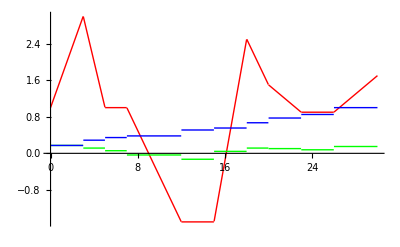

```mathematica
Plot[{f[x],p[x],P[x]},{x,0,30}, AxesOrigin->{0,0}, PlotRange->Full,PlotStyle->{{Red},{Green},{Blue}},PlotLegend->{"f(x)","PDF","CDF"}, LegendPosition->{1,0},LegendShadow->None]
```

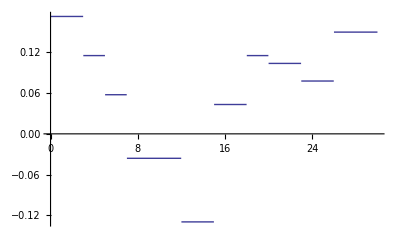

```mathematica
Plot[p[x], {x,0,30}]
```

```mathematica
f[x]
```

Piecewise[{{1.+0.666667 x, 0≤x<3}, {6.-x, 3≤x<5}, {1., 5≤x<7}, {4.5-0.5 x, 7≤x<12}, {-1.5, 12≤x<15}, {-21.5+1.33333 x, 15≤x<18}, {11.5-0.5 x, 18≤x<20}, {5.5-0.2 x, 20≤x<23}, {0.9, 23≤x<26}, {-4.3+0.2 x, 26≤x<30}}]

```mathematica
fNormed[x_]:=Simplify[f[x]/H]
```

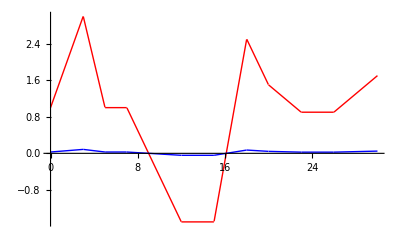

```mathematica
Plot[{f[x],fNormed[x]},{x,0,30}, AxesOrigin->{0,0}, PlotRange->Full,PlotStyle->{{Red},{Blue}},PlotLegend->{"f(x)","fNormed"}, LegendPosition->{1,0},LegendShadow->None]
```

```mathematica
fNormed[x]
```

Piecewise[{{-0.0431655, 12≤x<15}, {0.0258993, 23≤x<26}, {0.028777, 5≤x<7}, {0.172662-0.028777 x, 3≤x<5}, {0.129496-0.0143885 x, 7≤x<12}, {0.330935-0.0143885 x, 18≤x<20}, {0.158273-0.0057554 x, 20≤x<23}, {-0.123741+0.0057554 x, 26≤x<30}, {0.028777+0.0191847 x, 0≤x<3}, {-0.618705+0.0383693 x, 15≤x<18}}]

```mathematica
f[x]/H
```

0.028777 (Piecewise[{{1.+0.666667 x, 0≤x<3}, {6.-x, 3≤x<5}, {1., 5≤x<7}, {4.5-0.5 x, 7≤x<12}, {-1.5, 12≤x<15}, {-21.5+1.33333 x, 15≤x<18}, {11.5-0.5 x, 18≤x<20}, {5.5-0.2 x, 20≤x<23}, {0.9, 23≤x<26}, {-4.3+0.2 x, 26≤x<30}}])

```mathematica
H
```

34.75

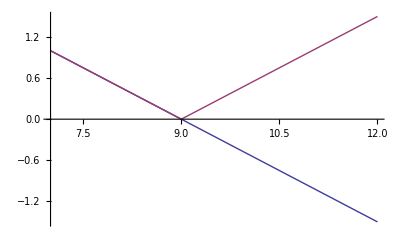

```mathematica
Plot[{Subscript[f, 4][x],Abs[Subscript[f, 4][x]]},{x,7,12}]
```

```mathematica
Subscript[f, 4][x]
```

4.5-0.5 x

```mathematica
Abs[Subscript[f, 4][x]]
```

Abs[4.5-0.5 x]